This notebook finds parameters to best fit the theoretical model of a DC motor to collected data.

Define constants

```mathematica
(* The maximum voltage of the motor. *)
motorVoltage=24;
```

```mathematica
(* The radius of the timing pulley on the axle of the motor in m. Multiplying an angle change by this value gives the distance the cart moves. *)
timingPulleyRadius=0.01051;
```

Import the data

```mathematica
dataDirectory=FileNameJoin[{NotebookDirectory[],"..","data"}];
```

```mathematica
dataPaths=FileNames["*.csv",dataDirectory];
```

```mathematica
(* The columns are index, time (in ns), and angle (in degrees) *)
data=Import[#,"csv"]&/@dataPaths;
```

Calculate the PWM duty cycles and voltages from the file names

```mathematica
dataFilenames=FileNameSplit[#][[-1]]&/@dataPaths;
```

```mathematica
pwms=If[StringPart[#,1]=="l",-1,1]FromDigits[StringJoin[StringPart[#,{2,3}]]]&/@dataFilenames;
```

```mathematica
voltages=N[(# /255)motorVoltage]&/@pwms;
```

Drop the index column, convert time to seconds, add voltage, and convert angle to cart position

```mathematica
data=MapIndexed[
Module[
{voltage=voltages[[#2[[1]]]]},
{N[#[[2]]/1*^6],voltage,timingPulleyRadius#[[3]]Degree}&/@#1
]&,
data
];
```

Calculate velocities

```mathematica
velocities={#[[2,1]],#[[2,2]],(#[[2,3]]-#[[1,3]])/(#[[2,1]]-#[[1,1]])}&/@Partition[#,2,1]&/@data;
```

Find the parameters that best fit the data

```mathematica
parameters=FindFit[Join@@velocities,a v(1-E^(-b t)),{a,b},{t,v}];
```

Plot the velocities and the fitted models

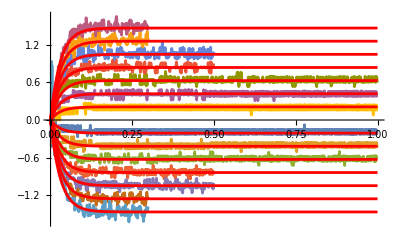

```mathematica
plot=GraphicsColumn[{
Text[a v (1-E^(-b t))/.parameters],
Show[
ListLinePlot[{#[[1]],#[[3]]}&/@#&/@velocities],
Plot[a v(1-E^(-b t))/.parameters/.v->#&/@voltages,{t,0,1},PlotStyle->Red]
]
}]
```

Uncomment to export an image of the plot

```mathematica
(*Export[
FileNameJoin[{NotebookDirectory[],"motor.png"}],
plot
];*)
```